# Best-experienced-payoff Dynamics

## Source code

### General options

```mathematica
Clear["Global`*"];
(* Symbols x, y, z and t must not be used in this notebook *)
SetOptions[Root,ExactRootIsolation->True];

precision=6;

ExpectedMove::invalidValueOf_testSetRule="the variable testSetRule in ExpectedMove[testSetRule, tieBreakingRule, n] cannot take the value `1`. It can only be \"all\", \"two\" or \"adj\"";
ExpectedMove::invalidValueOf_tieBreakingRule="the variable tieBreakingRule in ExpectedMove[testSetRule, tieBreakingRule, n] cannot take the value `1`. It can only be \"min\", \"stick\" or \"unif\"";
ExpectedMove::invalidValueOf_n="the variable n (number of nodes in the game) in ExpectedMove[testSetRule, tieBreakingRule, n] cannot take the value `1`. It must be an integer strictly greater than 1";
```

### Expected moves

#### Payoff and general functions

```mathematica
PayoffsX[n_]:=Module[{centipedePlus=3,centipedeMinus=1,gain,s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
gain=centipedePlus-centipedeMinus;
Table[If[j≥i,(i-1)*gain,(j-1)*gain-centipedeMinus],{i,s1},{j,s2}]
]

PayoffsY[n_]:=Module[{centipedePlus=3,centipedeMinus=1,gain,s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
gain=centipedePlus-centipedeMinus;
Table[If[j≥i+1,(i-1)*gain+centipedePlus,(j-1)*gain],{i,s2},{j,s1}]
]

ExpectedMove[testSetRule_,tieBreakingRule_ ,n_]:=Module[{},
If[Not[IntegerQ[n]] ||n<2,(Message[ExpectedMove::invalidValueOf_n,n];"Error parameterizing the length of the game (number of nodes must be at least 2)";Abort[])];
Switch[testSetRule,

"all",Switch[tieBreakingRule,
"min",ExpectedMoveAllMin[n,x,y],
"stick",ExpectedMoveAllStick[n,x,y],
"unif",ExpectedMoveAllUnif[n,x,y],
_,(Message[ExpectedMove::invalidValueOf_tieBreakingRule,tieBreakingRule];"Error parameterizing the tie-breaking rule";Abort[])
],

"two",Switch[tieBreakingRule,
"min",TieBreaker[i_,m_,j_,k_,payoffs_]:=MinIfTie[i,m,j,k,payoffs]; ExpectedMoveTwo[n,x,y],
"stick",ExpectedMoveTwoStick[n,x,y],
"unif",TieBreaker[i_,m_,j_,k_,payoffs_]:=UniformIfTie[i,m,j,k,payoffs];ExpectedMoveTwo[n,x,y],
_,(Message[ExpectedMove::invalidValueOf_tieBreakingRule,tieBreakingRule];"Error parameterizing the tie-breaking rule";Abort[])
],

"adj",Switch[tieBreakingRule,
"min",TieBreaker[i_,m_,j_,k_,payoffs_]:=MinIfTie[i,m,j,k,payoffs];ExpectedMoveAdjacent[n,x,y],
"stick",TieBreaker[i_,m_,j_,k_,payoffs_]:=StickToCurrent[i,m,j,k,payoffs];ExpectedMoveAdjacent[n,x,y],
"unif",TieBreaker[i_,m_,j_,k_,payoffs_]:=UniformIfTie[i,m,j,k,payoffs];ExpectedMoveAdjacent[n,x,y],
_,(Message[ExpectedMove::invalidValueOf_tieBreakingRule,tieBreakingRule];"Error parameterizing the tie-breaking rule";Abort[])
],

_,(Message[ExpectedMove::invalidValueOf_testSetRule,testSetRule];"Error parameterizing the test-set rule";Abort[])]
];

ExpectedMoveWithoutFirstVariables[testSetRule_,tieBreakingRule_ ,n_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],reducedEM},
reducedEM=ExpectedMove[testSetRule,tieBreakingRule,n];
reducedEM=Rest[Drop[reducedEM,{s1+1}]];
reducedEM/.{x[1]->1 - Sum[x[i],{i,2,s1}],y[1]->1 - Sum[y[i],{i,2,s2}]}
];

ExpectedMoveWithoutLastVariables[testSetRule_,tieBreakingRule_ ,n_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],reducedEM},
reducedEM=ExpectedMove[testSetRule,tieBreakingRule,n];
reducedEM=Most[Drop[reducedEM,{s1}]];
reducedEM/.{x[s1]->1 - Sum[x[i],{i,1,s1-1}],y[s2]->1 - Sum[y[i],{i,1,s2-1}]}
];

(* Tie breakers*)

MinIfTie[i_,m_,j_,k_,payoffs_]:=Module[{pim=payoffs[[i,m]],pjk=payoffs[[j,k]]},
Boole[pim>pjk||(pim==pjk&&i≤j)]
];

StickToCurrent[i_,m_,j_,k_,payoffs_]:=Module[{pim=payoffs[[i,m]],pjk=payoffs[[j,k]]},
Boole[pim>pjk]
];

UniformIfTie[i_,m_,j_,k_,payoffs_]:=Module[{pim=payoffs[[i,m]],pjk=payoffs[[j,k]]},
If[pim>pjk,1,If[pim==pjk,1/2,0]]
];
```

#### Test all

Min if tie

```mathematica
FirstMoversInflowAllMin[n_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
Table[(∑_(k=i)^s2 y[k])(∑_(m=1)^i y[m])^(s1-i)+∑_(k=2)^(i-1) y[k](∑_(l=1)^(k-1) y[l])^(i-k)(∑_(m=1)^k y[m])^(s1-i),{i,s1}]/.∑_(j=1)^s2 y[j]->1
];

SecondMoversInflowAllMin[n_,x_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
Join[{(∑_(k=2)^s1 x[k])(x[1]+x[2])^(s2-1)+x[1]^s2},
Table[(∑_(k=j+1)^s1 x[k])(∑_(m=1)^(j+1) x[m])^(s2-j)+∑_(k=2)^j x[k](∑_(l=1)^(k-1) x[l])^(j-k+1)(∑_(m=1)^k x[m])^(s2-j),{j,2,s2}]
]/.∑_(i=1)^s1 x[i]->1
];

ExpectedMoveAllMin[n_,x_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
Join[
FirstMoversInflowAllMin[n,y]-Table[x[i],{i,s1}],
SecondMoversInflowAllMin[n,x]-Table[y[j],{j,s2}]]
];
```

Stick if tie

```mathematica
StickToCurrentThenMinIfTie[q_,i_,m_,j_,k_,payoffs_]:=Module[{pim=payoffs[[i,m]],pjk=payoffs[[j,k]]},
Boole[pim>pjk||(pim==pjk&&(q==i||(i<j&&j≠q)))]
];

(*
MinIfTie[q_,i_,m_,j_,k_,payoffs_]:=Module[{pim=payoffs[[i,m]],pjk=payoffs[[j,k]]},
Boole[pim>pjk||(pim==pjk&&i≤j)]
];
*)

FirstMoversInflowAllStick[n_,x_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],payoffsX=PayoffsX[n]},
Table[(∑_(q=1)^s1 x[q]∑_(m=1)^s2 y[m]∏_(j=1)^s1 If[j==i,1,∑_(k=1)^s2 y[k]StickToCurrentThenMinIfTie[q,i,m,j,k,payoffsX]]),{i,s1}]/.∑_(j=1)^s2 y[j]->1
];

SecondMoversInflowAllStick[n_,x_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],payoffsY=PayoffsY[n]},
Table[(∑_(q=1)^s2 y[q]∑_(m=1)^s1 x[m]∏_(j=1)^s2 If[j==i,1,∑_(k=1)^s1 x[k]StickToCurrentThenMinIfTie[q,i,m,j,k,payoffsY]]),{i,s2}]/.∑_(j=1)^s1 x[j]->1
];

ExpectedMoveAllStick[n_,x_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
Join[
FirstMoversInflowAllStick[n,x,y]-Table[x[i],{i,s1}],
SecondMoversInflowAllStick[n,x,y]-Table[y[j],{j,s2}]]
];
```

Uniform if tie

```mathematica
FirstMoversInflowAllUnif[n_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
Table[(∑_(j=i)^s2 y[j])(∑_(j=1)^i y[j])^(s1-i)+∑_(k=2)^(i-1) y[k](∑_(j=1)^(k-1) y[j])∑_(j=0)^(s1-k-1) (Binomial[s1-k-1,j]*y[k]^j)/(j+1)(∑_(l=1)^(k-1) y[l])^(s1-k-1-j),{i,s1}]/.∑_(j=1)^s2 y[j]->1
];

SecondMoversInflowAllUnif[n_,x_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],X},
X=Table[0,{s2}];
X[[1]]=x[1]^s2/s2;
X=Join[{X[[1]]},Table[X[[1]]+∑_(k=2)^i x[k](∑_(j=1)^(k-1) x[j])∑_(j=0)^(s2-k) (Binomial[s2-k,j]*x[k]^j)/(j+1)(∑_(l=1)^(k-1) x[l])^(s2-k-j),{i,2,s2}]];
Table[(∑_(j=i+1)^s1 x[j])(∑_(j=1)^(i+1) x[j])^(s2-i)+X[[i]],{i,s2}]/.∑_(j=1)^s1 x[j]->1
];

ExpectedMoveAllUnif[n_,x_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
Join[
FirstMoversInflowAllUnif[n,y]-Table[x[i],{i,s1}],
SecondMoversInflowAllUnif[n,x]-Table[y[j],{j,s2}]]
];
```

#### Test two

```mathematica
ExpectedMoveTwo[n_,x_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],payoffsX=PayoffsX[n],payoffsY=PayoffsY[n]},
Join[
Table[(∑_(j=1)^s1 Boole[j≠i]∑_(k=1)^s2 ∑_(m=1)^s2 y[k] 1/(s1-1)y[m](x[j]TieBreaker[i,m,j,k,payoffsX]-x[i]TieBreaker[j,k,i,m,payoffsX])),{i,s1}],

Table[(∑_(j=1)^s2 Boole[j≠i]∑_(k=1)^s1 ∑_(m=1)^s1 x[k] 1/(s2-1)x[m](y[j]TieBreaker[i,m,j,k,payoffsY]-y[i]TieBreaker[j,k,i,m,payoffsY])),{i,s2}]
]/.{∑_(j=1)^s1 x[j]->1,∑_(j=1)^s2 y[j]->1}
];
```

Min if tie

```mathematica
(* Tie breaker defined in section "General functions" *)
```

Stick if tie

```mathematica
(* For a general case,we could use: *)
(*
StickToCurrent[i_,m_,j_,k_,payoffs_]:=Module[{pim=payoffs[[i,m]],pjk=payoffs[[j,k]]},
Boole[pim>pjk]
];
*)

ExpectedMoveTwoStick[n_,x_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
Join[
Table[1/(s1-1)∑_(h=1)^(i-1) ((∑_(k=h+1)^s2 ∑_(l=1)^s2 y[k]y[l]+∑_(k=2)^h ∑_(l=1)^(k-1) y[k]y[l])(x[i]+x[h])+x[i]∑_(k=1)^(h-1) y[k]^2)+1/(s1-1)∑_(h=i+1)^s1 ((∑_(k=i)^s2 ∑_(l=1)^i y[k]y[l]+∑_(k=2)^(i-1) ∑_(l=1)^(k-1) y[k]y[l])(x[i]+x[h])+x[i]∑_(k=1)^(i-1) y[k]^2)-x[i],{i,s1}],
Table[1/(s2-1)∑_(h=1)^(i-1) ((∑_(k=h+2)^s1 ∑_(l=1)^s1 x[k]x[l]+∑_(k=2)^(h+1) ∑_(l=1)^(k-1) x[k]x[l])(y[i]+y[h])+y[i]∑_(k=1)^h x[k]^2)+1/(s2-1)∑_(h=i+1)^s2 ((∑_(k=i+1)^s1 ∑_(l=1)^(i+1) x[k]x[l]+∑_(k=2)^i ∑_(l=1)^(k-1) x[k]x[l])(y[i]+y[h])+y[i]∑_(k=1)^i x[k]^2)-y[i],{i,s2}]
]/.{∑_(j=1)^s1 x[j]->1,∑_(j=1)^s2 y[j]->1}
];
```

Uniform if tie

```mathematica
(* Tie breaker defined in section "General functions" *)
```

#### Test adjacent

```mathematica
ExpectedMoveAdjacent[n_,x_,y_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],payoffsX=PayoffsX[n],payoffsY=PayoffsY[n]},
Join[Table[
If[i==s1,0,Switch[i,s1-1,1,_,1/2]x[i+1]∑_(k=1)^s2 ∑_(m=1)^s2 y[k]y[m]TieBreaker[i,m,i+1,k,payoffsX]]+If[i==1,0,Switch[i,2,1,_,1/2]x[i-1]∑_(k=1)^s2 ∑_(m=1)^s2 y[k]y[m]TieBreaker[i,m,i-1,k,payoffsX]]
-x[i]∑_(k=1)^s2 ∑_(m=1)^s2 y[k]y[m](
If[i==s1,0,Switch[i,1,1,_,1/2]TieBreaker[i+1,k,i,m,payoffsX]]+
If[i==1,0,Switch[i,s1,1,_,1/2]TieBreaker[i-1,k,i,m,payoffsX]]
)
,{i,1,s1}],

Table[
If[i==s2,0,Switch[i,s2-1,1,_,1/2]y[i+1]∑_(k=1)^s1 ∑_(m=1)^s1 x[k]x[m]TieBreaker[i,m,i+1,k,payoffsY]]+
If[i==1,0,Switch[i,2,1,_,1/2]y[i-1]∑_(k=1)^s1 ∑_(m=1)^s1 x[k]x[m]TieBreaker[i,m,i-1,k,payoffsY]]
-y[i]∑_(k=1)^s1 ∑_(m=1)^s1 x[k]x[m](
If[i==s2,0,Switch[i,1,1,_,1/2]TieBreaker[i+1,k,i,m,payoffsY]]+
If[i==1,0,Switch[i,s2,1,_,1/2]TieBreaker[i-1,k,i,m,payoffsY]]
),
{i,1,s2}]
]/.{∑_(j=1)^s1 x[j]->1,∑_(j=1)^s2 y[j]->1}
];
```

Min if tie

```mathematica
(* Tie breaker defined in section "General functions" *)
```

Stick if tie

```mathematica
(* Tie breaker defined in section "General functions" *)
```

Uniform if tie

```mathematica
(* Tie breaker defined in section "General functions" *)
```

### Jacobians

```mathematica
JacobianOfExpectedMove[EM_]:=Module[{n=Length[EM]-2,s1,s2},
s1=IntegerPart[(n+3)/2];s2=IntegerPart[(n+2)/2];
D[EM,{Join[Table[x[i],{i,s1}],Table[y[j],{j,s2}]]}]
];

ProjectedJacobian[EM_]:=Module[{n=Length[EM]-2,s1,s2,Φ1,Φ2},
s1=IntegerPart[(n+3)/2];s2=IntegerPart[(n+2)/2];
Φ1=IdentityMatrix[s1]-1/s1 ConstantArray[1,{s1,s1}];
Φ2=IdentityMatrix[s2]-1/s2 ConstantArray[1,{s2,s2}];
ArrayFlatten[{{Φ1,0},{0,Φ2}}].JacobianOfExpectedMove[EM].ArrayFlatten[{{Φ1,0},{0,Φ2}}]
];
```

### Exact rest points (Gröbner bases)

```mathematica
ExactRestPoints[testSetRule_,tieBreakingRule_ ,n_,verbosity_:5,prec_:precision]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],EM,vars,basis,sol},
EM=ExpectedMove[testSetRule,tieBreakingRule ,n];
If[verbosity≥5,
Print["Expected Move: \n", MatrixForm@EM]
];

If[tieBreakingRule=="stick",
(* We have to remove the vertex *)
Print["IMPORTANT: To get a polynomial system with a finite solution set we have to impose the additional restriction x[1]≠1.\nThis is done by adding the polynomial (x[1]-1)*z==1.\nThus, even though x[1]=y[1]=1 is indeed a rest point, it will not appear below."];  
vars=Join[Table[x[i],{i,s1}],Table[y[i],{i,s2}],{z}];
basis=GroebnerBasis[Join[
{EM==ConstantArray[0,Length[EM]]},{(x[1]-1)*z==1},
{Sum[x[i],{i,s1}]==1,Sum[y[j],{j,s2}]==1}],
vars];
,
vars=Join[Table[x[i],{i,s1}],Table[y[i],{i,s2}]];
basis=GroebnerBasis[Join[
{EM==ConstantArray[0,Length[EM]]},
{Sum[x[i],{i,s1}]==1,Sum[y[j],{j,s2}]==1}],
vars];
];

If[verbosity≥4,
Print["Gröbner basis: \n", MatrixForm@basis]
];

If[verbosity≥2,
Print["Variables in Gröbner basis: \n",Map[Variables,basis]];
Print["Max degrees in Gröbner basis:"];
Print[MatrixForm@Prepend[Map[Exponent[#,vars]&,basis],vars]];
];

sol={ToRules[
Reduce[Join[{basis==ConstantArray[0,Length[basis]]},Table[0≤x[i]≤1,{i,s1}],Table[0≤y[j]≤1,{j,s2}]],Reals,Backsubstitution->True]
]};

If[verbosity≥1,
Print["Numerical approximation to exact solution computed using the Gröbner basis: \n", (sol/.{((x[i_Integer]->num_):>(x[i]->N[num,prec])),((y[i_Integer]->num_):>(y[i]->N[num,prec])),((z->num_):>(z->N[num,prec]))})];
];

sol
];

NExactRestPoints[testSetRule_,tieBreakingRule_ ,n_,verbosity_:3,prec_:precision]:=Module[{sol},
sol=ExactRestPoints[testSetRule,tieBreakingRule,n,verbosity,prec];
If[verbosity≥3,
Print["Exact solution of Gröbner basis in the simplex: \n", sol];
];
(sol/.{((x[i_Integer]->num_):>(x[i]->N[num,prec])),((y[i_Integer]->num_):>(y[i]->N[num,prec])),((z->num_):>(z->N[num,prec]))})
]
```

### Approximate rest points (floating-point and rational approximations)

```mathematica
ClipTo01[v_]:=If[v<0,0,If[v>1,1,v]];
SetAttributes[ClipTo01,Listable];

ProjectOnSimplex[v_]:=Normalize[ClipTo01[v],Total];

FloatingPointApproximateRestPoint[testSetRule_,tieBreakingRule_ ,n_,step_:2.^-4]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],EM,Φ1,Φ2,P,vars,CompiledNextIteration,Compiledfpoint},
EM=ExpectedMove[testSetRule,tieBreakingRule ,n];

Φ1=IdentityMatrix[s1]-1/s1 ConstantArray[1,{s1,s1}];
Φ2=IdentityMatrix[s2]-1/s2 ConstantArray[1,{s2,s2}];
P=ArrayFlatten[{{Φ1,0},{0,Φ2}}];
vars=Join[Table[x[i],{i,s1}],Table[y[i],{i,s2}]];

CompiledNextIteration=Compile[Evaluate[vars],Evaluate[Join[ProjectOnSimplex[Table[x[i],{i,s1}]],ProjectOnSimplex[Table[y[i],{i,s2}]]]+step*P.EM]];

Compiledfpoint=Clip[FixedPoint[(CompiledNextIteration@@#)&,Join[ConstantArray[1./s1,s1],ConstantArray[1./s2,s2]],10^4,SameTest->(Norm[#1-#2]<10^-20&)],{0,1}];

Thread[vars->Compiledfpoint]

];

RationalApproximateRestPoint[testSetRule_,tieBreakingRule_ ,n_,verbosity_:1,step_:1,minIterations_:1,maxIterations_:200]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],EM,fixedPoint,iterations,oldFixedPointStr="old",newFixedPointStr="new",vars,scientificDigits=3,decimalPlaces=6,headings,Nice},
vars=Join[Table[x[i],{i,s1}],Table[y[i],{i,s2}]];

EM=ExpectedMove[testSetRule,tieBreakingRule ,n];

fixedPoint=vars/.FloatingPointApproximateRestPoint[testSetRule,tieBreakingRule ,n];

Nice[a_]:=If[a<10^-4,ScientificForm[N[a],scientificDigits],NumberForm[N[a],{decimalPlaces+4,decimalPlaces}]];
SetAttributes[Nice,Listable];

If[verbosity≥1,
headings={Join[
Table[Row[{Style["x[",Bold,FontFamily->"Palatino",Italic,14],Style[i,Bold,FontFamily->"Palatino",14],Style["]",Bold,FontFamily->"Palatino",14]}],{i,s1}],Table[Row[{Style["y[",Bold,FontFamily->"Palatino",Italic,14],Style[i,Bold,FontFamily->"Palatino",14],Style["]",Bold,FontFamily->"Palatino",14]}],{i,s2}]],None};
Print["\nFloating-point approximation to rest point:\n\t",TableForm[Nice[fixedPoint],TableHeadings->headings,TableDirections->Row,TableSpacing->{3,Automatic}]];
];

For[iterations=1,iterations≤minIterations||(iterations≤maxIterations&&(oldFixedPointStr≠newFixedPointStr)),iterations++,

(* The following three lines of code should not be necessary in principle, but they are vital to speed up the execution *)
fixedPoint=N[fixedPoint,16]; 
(* Here we are taking the 16 most significant digits of fixedPoint, which is a rational (except at the very first iteration, where it is a machine number). *)
(* fixedPoint now is NOT an IEEE 754 floating-point number (except at the very first iteration); it is a number with 16 digits of precision, and will be rationalized at the next line of code *)
fixedPoint=Rationalize[fixedPoint,0];
fixedPoint=Join[Normalize[fixedPoint[[;;s1]],Total],Normalize[fixedPoint[[s1+1;;]],Total]];

oldFixedPointStr=ToString[Nice[fixedPoint]];
fixedPoint=fixedPoint + (EM/.(Thread[vars->fixedPoint]));
newFixedPointStr=ToString[Nice[fixedPoint]];

If[verbosity≥1,
Print["\n",iterations ," iterations with rational arithmetic conducted:\n\t",TableForm[Nice[fixedPoint],TableHeadings->headings,TableDirections->Row,TableSpacing->{3,Automatic}]];
];

];

(* When we go out of the loop For above because (oldFixedPointStr == newFixedPointStr), we know that we have found a rational point x such that Nice[x] == Nice[x + (EM/.(Thread[vars->x]))], with all the operations conducted using (exact) rational arithmetic *)

Thread[vars->fixedPoint]
];
```

### Eigenvalues at approximate rest points

```mathematica
EigenvaluesAtRationalApproximateRestPoint[testSetRule_,tieBreakingRule_ ,n_,verbosity_:1]:=Module[{projectedJacobian,fixedPointRules,eigenvalues,scientificDigits=3,decimalPlaces=4,niceEigenvalues,Nice},

projectedJacobian=ProjectedJacobian[ExpectedMove[testSetRule,tieBreakingRule ,n]];
fixedPointRules=RationalApproximateRestPoint[testSetRule,tieBreakingRule ,n,verbosity];
eigenvalues=Eigenvalues[projectedJacobian/.fixedPointRules];

If[verbosity≥1,
Nice[a_]:=If[Abs[a]<10^-2,ScientificForm[a,scientificDigits],NumberForm[a,{decimalPlaces+4,decimalPlaces}]];
niceEigenvalues=Map[(Nice[Re[#]]+Nice[Im[#]]*I)&,N[eigenvalues,16]];
Print["Approximate eigenvalues:\n",TableForm[niceEigenvalues,TableHeadings->{Table[Style["λ"<>ToString[i],Bold,14],{i,n+2}],None},TableDirections->Row,TableSpacing->{3,Automatic}]];
];

eigenvalues
];
```

### Local stability of interior rest point (perturbation theorem)

```mathematica
LocalStabilityOfInteriorRestPoint[testSetRule_,tieBreakingRule_ ,n_,verbosity_:5,prec_:precision]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],interiorRestPoint,projectedJacobian,closeRational,eigensystem,eigenvalues,eigenvectors,tolerance,xVector,yVector},
xVector=Table[x[i],{i,s1}];
yVector=Table[y[i],{i,s2}];

interiorRestPoint=Select[ExactRestPoints[testSetRule,tieBreakingRule ,n,verbosity],((x[1]/.#)≠1)&];

If[Length[interiorRestPoint]>0,
interiorRestPoint=First[interiorRestPoint];

If[verbosity≥1,
Print["Numerical approximation to interior exact solution: \n", (interiorRestPoint/.{((x[i_Integer]->num_):>(x[i]->N[num,prec])),((y[i_Integer]->num_):>(y[i]->N[num,prec])),((z->num_):>(z->N[num,prec]))})]
];

projectedJacobian=ProjectedJacobian[ExpectedMove[testSetRule,tieBreakingRule ,n]];

closeRational=Thread[Join[xVector,yVector]-> Join[
Normalize[Rationalize[N[xVector/.interiorRestPoint,10],0],Total],
Normalize[Rationalize[N[yVector/.interiorRestPoint,10],0],Total]
]];

If[verbosity≥4,
Print["Rational point close to interior exact solution: \n", closeRational];
];
If[verbosity≥2,
Print["Numerical approximation to rational point close to interior exact solution: \n", N[closeRational]];
];

eigensystem=Eigensystem[projectedJacobian/.closeRational];
eigenvalues=First[eigensystem];
eigenvectors=Last[eigensystem];

If[verbosity≥6,Print["Eigenvalues at close rational point:\n",eigenvalues]];
If[verbosity≥1,Print["N@ Eigenvalues at close rational point:\n",N@eigenvalues]];

If[verbosity≥6,Print["Eigenvectors at close rational point (in rows):\n",MatrixForm@eigenvectors]];
If[verbosity≥5,Print["N@ Eigenvectors at close rational point (in rows):\n",MatrixForm[N[eigenvectors]]]];
 
If[Length[eigenvectors]≠n+2,Print["WARNING! Number of eigenvectors ≠ Number of dimensions"]];

If[verbosity≥1,Print["Computing tolerance... "]];

Block[{$MaxExtraPrecision=50},
tolerance=N[Norm[eigenvectors,∞],40]*N[Norm[Simplify[(projectedJacobian/.closeRational)-(projectedJacobian/.interiorRestPoint)],∞],40]*N[Norm[Inverse[eigenvectors],∞],40]
];

If[verbosity≥1,Print["Tolerance computed with perturbation theorem: ",tolerance]];
If[verbosity≥4,
Print["Precision of tolerance: ",Precision[tolerance]];
Print["Accuracy of tolerance: ",Accuracy[tolerance]];
Print["Real Digits of tolerance: ",RealDigits[tolerance]];
];

If[verbosity≥1,Print["The real part of the relevant eigenvalues at the interior rest point is no more than:\n",N[eigenvalues[[;;-3]] ,6]+ 10*tolerance]];

If[Not@Reduce[{Or@@MapThread[#1≥#2&,{Re[eigenvalues[[;;-3]] + 10*Rationalize[tolerance,0]],ConstantArray[0,Length[eigenvalues[[;;-3]]]]}]},Reals]
,
Print["Apart from the two zero eigenvalues, all eigenvalues have strictly negative real part"];
Return["The interior rest point is (locally) asymptotically stable"];
,
Print["There seems to be at least one eigenvalue with positive real part"];
Return["Local stability analysis is inconclusive"];
];

,
Return["There is no interior rest point"];
];

];
```

### Global stability of interior rest point (exact Lyapunov function)

```mathematica
GlobalStabilityOfInteriorRestPoint[testSetRule_,tieBreakingRule_ ,n_,verbosity_:1,prec_:precision]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],interiorRestPointRules,interiorRestPoint,reducedInteriorRestPoint,otherPointsWhereDerivativeEquals0,xVector,yVector},
xVector=Table[x[i],{i,s1}];
yVector=Table[y[i],{i,s2}];

interiorRestPointRules=Select[ExactRestPoints[testSetRule,tieBreakingRule ,n,verbosity],((x[1]/.#)≠1)&];

If[Length[interiorRestPointRules]>0,
interiorRestPointRules=First[interiorRestPointRules];

If[verbosity≥1,
Print["Numerical approximation to interior exact solution: \n", (interiorRestPointRules/.{((x[i_Integer]->num_):>(x[i]->N[num,prec])),((y[i_Integer]->num_):>(y[i]->N[num,prec])),((z->num_):>(z->N[num,prec]))})]
];

If[testSetRule=="two"&&tieBreakingRule=="min",

(*Distance to interior rest point*)
interiorRestPoint=Join[xVector,yVector]/.interiorRestPointRules;

If[verbosity≥1,
Print["Lyapunov function: euclidean distance to interior rest point, i.e. distance to:\n", interiorRestPointRules];
Print["\twith numerical approximation:\n\t",Thread[Join[xVector,yVector]->N@interiorRestPoint]];
Print["Checking whether the derivative of the Lyapunov function is always different from zero (except at the rest points)..."];
];

otherPointsWhereDerivativeEquals0=CylindricalDecomposition[Join[{ExpectedMove[testSetRule,tieBreakingRule,n].(Join[xVector,yVector]-interiorRestPoint)==0},
Table[0≤x[i]≤1,{i,s1}],Table[0≤y[i]≤1,{i,s2}],
{Total[xVector]==1,Total[yVector]==1},
{Join[xVector,yVector]≠interiorRestPoint},
{Join[xVector,yVector]≠Join[{1},ConstantArray[0,s1-1],{1},ConstantArray[0,s2-1]]}
]
,Join[xVector,yVector]];

,
(*Reduced Distance to interior rest point*)
reducedInteriorRestPoint=Join[Rest[xVector],Rest[yVector]]/.interiorRestPointRules;

If[verbosity≥1,
Print["Lyapunov function: euclidean distance to interior rest point ignoring x[1] and y[1], i.e. distance to:\n", Thread[Join[Rest[xVector],Rest[yVector]]->reducedInteriorRestPoint]];
Print["\twith numerical approximation:\n\t",Thread[Join[Rest[xVector],Rest[yVector]]->N@reducedInteriorRestPoint]];
Print["Checking whether the derivative of the Lyapunov function is always different from zero (except at the rest points)..."];
];

otherPointsWhereDerivativeEquals0=CylindricalDecomposition[Join[{ExpectedMoveWithoutFirstVariables[testSetRule,tieBreakingRule,n].(Join[Rest[xVector],Rest[yVector]]-reducedInteriorRestPoint)==0},
Table[0≤x[i]≤1,{i,2,s1}],Table[0≤y[i]≤1,{i,2,s2}],
(*{Sum[x[i],{i,2,s1}]≤1,Sum[y[i],{i,2,s2}]≤1},*)
{Join[Rest[xVector],Rest[yVector]]≠reducedInteriorRestPoint},
{Join[Rest[xVector],Rest[yVector]]≠ConstantArray[0,n]}
]
,Join[Rest[xVector],Rest[yVector]]];
];

If[otherPointsWhereDerivativeEquals0===False,
If[verbosity≥1,Print["The derivative of the Lyapunov function is always different from zero (except at the rest points)"]];
Return["The interior point is almost globally asymptotically stable"]
,
If[verbosity≥1,
Print["There are other points where the derivative of the Lyapunov function equals 0:\n",otherPointsWhereDerivativeEquals0];
Print["\twith numerical approximation:\n\t",N@otherPointsWhereDerivativeEquals0];
];
Return["Global stability analysis is inconclusive"];
];

,
Return["There is no interior rest point"];
];

];
```

### Initial conditions

```mathematica
RandomPoints::usage="RandomPoints[n, nPoints] returns a list of nPoints random points for a centipede game of length n" ;
RandomPoints[n_,nPoints_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},MapThread[Join,{Map[#/Total[#]&,Table[RandomReal[1,s1],nPoints]],Map[#/Total[#]&,Table[RandomReal[1,s2],nPoints]]}]
];

SimplexMesh::usage="SimplexMesh[nStrategies, nAgents] returns a list of all the possible strategy distributions in a population of nAgents agents who can choose one of nStrategies possible strategies. The number of possible distributions is Binomial[nAgents+nStrategies-1,nAgents]" ;
SimplexMesh[nStrategies_,nAgents_]:=Flatten[Permutations/@IntegerPartitions[nAgents,{nStrategies},Range[0,nAgents]],1]/N@nAgents;

MeshPoints::usage="MeshPoints[n, nAgentsPerPopulation] returns a list of all the possible states in a centipede game of length n with nAgentsPerPopulation agents in each population. The number of possible distributions is Binomial[nAgents + IntegerPart[(n+3)/2] - 1,nAgents]*" ;
MeshPoints[n_,nAgentsPerPopulation_]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2]},
Flatten[Outer[Join,SimplexMesh[s1,nAgentsPerPopulation],SimplexMesh[s2,nAgentsPerPopulation],1],1]
];
```

### Numerical global stability of interior rest point (numerical evaluation of an approximate Lyapunov function)

```mathematica
NumericalGlobalStabilityOfInteriorRestPointLyapunov[testSetRule_,tieBreakingRule_ ,n_,points_,verbosity_:1,samplesPerPack_:10^5]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],interiorFPRestPoint,vars,packs,CompiledVdot,valuesOfVdot,pos,nonNegativeValuePoints={},p=1},

vars=Join[Table[x[i],{i,s1}],Table[y[i],{i,s2}]];

interiorFPRestPoint=vars/.FloatingPointApproximateRestPoint[testSetRule,tieBreakingRule ,n];

If[verbosity≥1,
Print["Numerical (floating-point) approximation to interior exact solution: \n", Thread[vars->interiorFPRestPoint]]
];

packs=Partition[points,UpTo[samplesPerPack]];

(*Distance to interior rest point*)

If[verbosity≥1,
Print["Lyapunov function: euclidean distance to (floating-point approximation to) the interior rest point."];
Print["We now evaluate the derivative of the Lyapunov function at ", Length[points], " points using (IEEE 754) floating-point arithmetic, in packs of up to ",samplesPerPack," points."];
];

CompiledVdot=Compile[
Evaluate[vars],
Evaluate[ExpectedMove[testSetRule,tieBreakingRule ,n].(vars-interiorFPRestPoint)]
];

Scan[Function[pack,

valuesOfVdot=ParallelMap[(CompiledVdot@@#)&,pack];

If[verbosity≥1,
Print["Pack ", p,"; Size of pack: ", Length@pack];p++;
];

If[verbosity≥2,
Print["\tFirst ",Min[10,Length[pack]]," points in pack:\t", MatrixForm[pack[[1;;Min[10,Length[pack]]]]]];
Print["\t... and their values of Vdot:\t",MatrixForm[valuesOfVdot[[1;;Min[10,Length[pack]]]]]];
];

pos=Position[valuesOfVdot,_?NonNegative];
If[pos≠{},
Print["\tNonnegative values of vdot found at: "];
Print["\t\tPoints: ",Map[Thread[vars->#]&,Extract[pack,pos]]];
Print["\t\tValues: ",Extract[valuesOfVdot,pos]];
nonNegativeValuePoints=Join[nonNegativeValuePoints,Map[Thread[vars->#]&,Extract[pack,pos]]];
,
If[verbosity≥1,Print["\tAll values in the pack are negative\n"]];
];

pos=Position[valuesOfVdot,x_/;x>-10^-15];
If[pos≠{},
Print["\tValues of vdot greater than -10^-15 found at: "];
Print["\t\tPoints: ",Map[Thread[vars->#]&,Extract[pack,pos]]];
Print["\t\tValues: ",Extract[valuesOfVdot,pos]];
,
If[verbosity≥3,Print["\tAll values are below -10^-15\n"]];
];
],packs];

If[Length[nonNegativeValuePoints]>0,
If[verbosity≥1,Print["Below you can see the points we have found where the derivative of the Lyapunov function is non-negative. If you can see other points beside the \"stop-immediately\" rest point, that means that the chosen function is not a Lyapunov function. Alternatively, if there are no points below, or if the only point below is the \"stop-immediately\" rest point, then this means that we have not found numerical evidence that contradicts the hypothesis that the interior point is almost globally asymptotically stable. In other words, this computation would suggest that the interior rest point might be almost globally asymptotically stable."]];
Return[nonNegativeValuePoints];
,
If[verbosity≥1,Print["The derivative of the Lyapunov function is negative in all evaluated points."]];
Return[StringJoin["We have evaluated ",ToString[Length[points]]," points and we have not found numerical evidence that contradicts the hypothesis that the interior point is almost globally asymptotically stable. In other words, this computation suggests that the interior rest point might be almost globally asymptotically stable"]];
];

];
```

### Numerical global stability of interior rest point (NDSolve)

```mathematica
NumericalGlobalStabilityOfInteriorRestPointNDSolve[testSetRule_,tieBreakingRule_ ,n_,points_,verbosity_:1,samplesPerPack_:10^3,time_:200,tolerance_:10.^-4,accuracyGoal_:6]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],interiorFPRestPoint,vars,rulesToAddt,varsWitht,packs,Dvars,projectedEM,p=1,FinalPoint,finalPoints,problematicPoints={}},

SetSharedVariable[problematicPoints]; (*So we can use ParallelMap*)

vars=Join[Table[x[i],{i,s1}],Table[y[i],{i,s2}]];
rulesToAddt={x[i_Integer]->x[i][t],y[i_Integer]->y[i][t]};
varsWitht=vars/.rulesToAddt;
Dvars=Join[Table[x[i]'[t],{i,s1}],Table[y[i]'[t],{i,s2}]];

interiorFPRestPoint=vars/.FloatingPointApproximateRestPoint[testSetRule,tieBreakingRule ,n];

If[verbosity≥1,
Print["Numerical (floating-point) approximation to interior exact solution: \n", Thread[vars->interiorFPRestPoint]]
];

projectedEM=ArrayFlatten[{{IdentityMatrix[s1]-1/s1 ConstantArray[1,{s1,s1}],0},{0,IdentityMatrix[s2]-1/s2 ConstantArray[1,{s2,s2}]}}].(ExpectedMove[testSetRule,tieBreakingRule,n]/.rulesToAddt);


packs=Partition[points,UpTo[samplesPerPack]];

(*NDSolve*)

If[verbosity≥1,
Print["We now solve the differential equation numerically (with NDSolve), starting at each of the ", Length[points], " points provided, in packs of up to ",samplesPerPack," points."];
];

FinalPoint[initialPoint_]:=Module[{finalTime=time,sol},
sol=NDSolveValue[
{Thread[Dvars==projectedEM],Thread[(varsWitht/.t->0)==initialPoint],WhenEvent[Evaluate[Norm[varsWitht-interiorFPRestPoint]<tolerance], "StopIntegration";finalTime=t]},
vars,{t,0,time},AccuracyGoal->accuracyGoal];

If[verbosity≥10,Print[Plot[Evaluate@MapThread[Tooltip,{Map[#[t]&,sol],vars}],{t,0,finalTime},PlotLegends->vars]]];

If[finalTime≥time,
Print["Fixed point not reached:\n\t",initialPoint,"\n\t-> ",Map[#[finalTime]&,sol]];
AppendTo[problematicPoints,initialPoint->Map[#[finalTime]&,sol]];
];
Map[#[finalTime]&,sol]
];

Scan[Function[pack,

finalPoints=ParallelMap[FinalPoint,pack]; 
(*If you want graphics, you need to replace ParallelMap with Map *)

If[verbosity≥1,
Print["Pack ", p,"; Size of pack: ", Length@pack];p++;
];

If[verbosity≥2,
Print["\tFirst ",Min[10,Length[pack]]," initial points in pack:\t", MatrixForm[pack[[1;;Min[10,Length[pack]]]]]];
Print["\t... and their corresponding final points:\t",MatrixForm[finalPoints[[1;;Min[10,Length[pack]]]]]];
];

If[verbosity≥3,
Print["\tProblematic points so far:\t", MatrixForm[problematicPoints]];
];

],packs];

If[Length[problematicPoints]>0,
If[verbosity≥1,Print["We have found initial points that did not lead to the proximities of the interior rest point. The following are the problematic initial conditions and their corresponding end points. If you can see other points beside the \"stop-immediately\" initial condition, you may want to try again with a greater value of time or a greater value of tolerance."]];
Return[problematicPoints];
,
If[verbosity≥1,Print["All initial points evaluated led to the proximities of the interior rest point."]];
Return[StringJoin["We have evaluated ",ToString[Length[points]]," initial points and we have not found numerical evidence that contradicts the hypothesis that the interior point is almost globally asymptotically stable. In other words, this computation suggests that the interior rest point might be almost globally asymptotically stable"]];
];

];
```

### Solve mean dynamics

```mathematica
NDSolveMeanDynamics[testSetRule_,tieBreakingRule_ ,n_,ip_:{},verbosity_:1,time_:300,tolerance_:10.^-4,accuracyGoal_:6]:=Module[{s1=IntegerPart[(n+3)/2],s2=IntegerPart[(n+2)/2],interiorFPRestPoint,vars,rulesToAddt,varsWitht,Dvars,projectedEM,FinalPoint,sol,finalTime,initialPoint},

If[ip=={},initialPoint=First[RandomPoints[n,1]],initialPoint=ip];

vars=Join[Table[x[i],{i,s1}],Table[y[i],{i,s2}]];
rulesToAddt={x[i_Integer]->x[i][t],y[i_Integer]->y[i][t]};
varsWitht=vars/.rulesToAddt;
Dvars=Join[Table[x[i]'[t],{i,s1}],Table[y[i]'[t],{i,s2}]];

interiorFPRestPoint=vars/.FloatingPointApproximateRestPoint[testSetRule,tieBreakingRule ,n];

If[verbosity≥1,
Print["Numerical (floating-point) approximation to interior exact solution: \n", Thread[vars->interiorFPRestPoint]]
];
projectedEM=ArrayFlatten[{{IdentityMatrix[s1]-1/s1 ConstantArray[1,{s1,s1}],0},{0,IdentityMatrix[s2]-1/s2 ConstantArray[1,{s2,s2}]}}].(ExpectedMove[testSetRule,tieBreakingRule,n]/.rulesToAddt);

(*NDSolve*)

If[verbosity≥1,
Print["We now solve the differential equation numerically (with NDSolve), starting at the initial point: ", initialPoint];
];

finalTime=time;

sol=NDSolveValue[
{Thread[Dvars==projectedEM],Thread[(varsWitht/.t->0)==initialPoint],WhenEvent[Evaluate[Norm[varsWitht-interiorFPRestPoint]<tolerance], "StopIntegration";finalTime=t]},
vars,{t,0,time},AccuracyGoal->accuracyGoal];

If[verbosity≥2,Print[Plot[Evaluate@MapThread[Tooltip,{Map[#[t]&,sol],vars}],{t,0,finalTime},PlotLegends->vars]]];

If[verbosity≥1,
Print@Row[{
Plot[Evaluate@MapThread[Tooltip,{Map[#[t]&,sol[[;;s1]]],vars[[;;s1]]}],{t,0,finalTime},PlotLegends->vars[[;;s1]],PlotLabel->"First mover",ImageSize->Medium],
Plot[Evaluate@MapThread[Tooltip,{Map[#[t]&,sol[[s1+1;;]]],vars[[s1+1;;]]}],{t,0,finalTime},PlotLegends->vars[[s1+1;;]],PlotLabel->"Second mover",ImageSize->Medium]
},"                ", Frame->True,FrameMargins->15,RoundingRadius->15];
];

If[finalTime≥time,
Print["Fixed point not reached:\n\t",initialPoint,"\n\t-> ",Map[#[finalTime]&,sol]];
];

{initialPoint,sol,finalTime,Map[#[finalTime]&,sol]}

];
```

## Parameterization

```mathematica
testSetRule="all"; (* Possible values are "all", "two" or "adj" *)
tieBreakingRule="min"; (* Possible values are "min", "stick" or "unif" *)
n=3; (* n is the number of nodes in the Centipede game *)
```

## Examples of usage

Numerical (floating-point) approximation to interior exact solution: 
{x[1]→0.,x[2]→0.,x[3]→0.,x[4]→3.56179×10^-9,x[5]→0.000593399,x[6]→0.0580716,x[7]→0.281957,x[8]→0.343249,x[9]→0.242263,x[10]→0.0738669,y[1]→0.,y[2]→0.,y[3]→2.13661×10^-14,y[4]→6.00232×10^-6,y[5]→0.0101091,y[6]→0.162311,y[7]→0.338578,y[8]→0.276597,y[9]→0.164572,y[10]→0.047827}

We now solve the differential equation numerically (with NDSolve), starting at the initial point: {0.99,0.01,0,0,0,0,0,0,0,0,0.99,0.01,0,0,0,0,0,0,0,0}

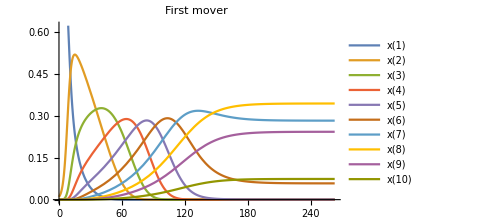
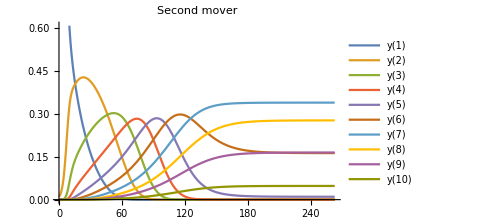

{{0.99,0.01,0,0,0,0,0,0,0,0,0.99,0.01,0,0,0,0,0,0,0,0},{InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>]},262.77,{-2.83972×10^-17,7.90029×10^-17,-5.27656×10^-17,3.58701×10^-9,0.00059472,0.0581115,0.281991,0.343217,0.242228,0.0738573,-6.63278×10^-16,1.3546×10^-15,2.03876×10^-14,6.02615×10^-6,0.0101217,0.162367,0.338572,0.276561,0.16455,0.0478218}}

Numerical (floating-point) approximation to interior exact solution: 
{x[1]→0.,x[2]→0.,x[3]→0.,x[4]→3.56179×10^-9,x[5]→0.000593399,x[6]→0.0580716,x[7]→0.281957,x[8]→0.343249,x[9]→0.242263,x[10]→0.0738669,y[1]→0.,y[2]→0.,y[3]→2.13661×10^-14,y[4]→6.00232×10^-6,y[5]→0.0101091,y[6]→0.162311,y[7]→0.338578,y[8]→0.276597,y[9]→0.164572,y[10]→0.047827}

We now solve the differential equation numerically (with NDSolve), starting at the initial point: {0.082952,0.110915,0.0881323,0.103171,0.085021,0.130991,0.153966,0.00412889,0.0745872,0.166135,0.106181,0.137697,0.110937,0.0853716,0.0859992,0.0669053,0.157488,0.100291,0.0497905,0.0993388}

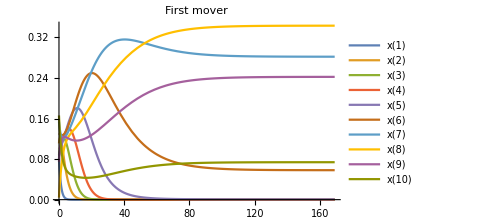
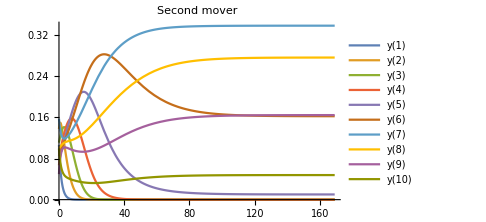

{{0.082952,0.110915,0.0881323,0.103171,0.085021,0.130991,0.153966,0.00412889,0.0745872,0.166135,0.106181,0.137697,0.110937,0.0853716,0.0859992,0.0669053,0.157488,0.100291,0.0497905,0.0993388},{InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>],InterpolatingFunction[{{0., 300.}}, <>]},169.006,{-7.6338×10^-10,1.52676×10^-9,-1.52676×10^-9,5.1115×10^-9,0.000594717,0.0581115,0.281991,0.343218,0.242228,0.0738574,-3.51255×10^-9,7.02509×10^-9,-7.02508×10^-9,6.03311×10^-6,0.0101217,0.162367,0.338572,0.276561,0.164551,0.0478216}}

```mathematica
testSetRule="adj"; (* Possible values are "all", "two" or "adj" *)
tieBreakingRule="min"; (* Possible values are "min", "stick" or "unif" *)
n=18; (* n is the number of nodes in the Centipede game *)
verbosity=1; (* the higher the value of verbosity, the more messages are printed along the execution of any function. 0 prints no messages. 10 prints all implemented messages *)
nAgentsPerPopulation=4;

(*MatrixForm[ExpectedMove[testSetRule,tieBreakingRule,n]]
MatrixForm[JacobianOfExpectedMove@ExpectedMove[testSetRule,tieBreakingRule,n]]
MatrixForm[ProjectedJacobian@ExpectedMove[testSetRule,tieBreakingRule,n]]
MatrixForm@ExpectedMoveWithoutFirstVariables[testSetRule,tieBreakingRule,n]
MatrixForm@FullSimplify[ExpectedMoveWithoutLastVariables[testSetRule,tieBreakingRule,n]]

EM=ExpectedMove[testSetRule,tieBreakingRule,n]
EM=ExpectedMoveWithoutLastVariables[testSetRule,tieBreakingRule,n]*)

(*a=ExactRestPoints[testSetRule,tieBreakingRule,n,4]*)
(*NExactRestPoints[testSetRule,tieBreakingRule,n,0]
FloatingPointApproximateRestPoint[testSetRule,tieBreakingRule,10];

RationalApproximateRestPoint[testSetRule,tieBreakingRule,n];
*)
(*EigenvaluesAtRationalApproximateRestPoint[testSetRule,tieBreakingRule,6];

(*LocalStabilityOfInteriorRestPoint[testSetRule,tieBreakingRule,3,10]*)
GlobalStabilityOfInteriorRestPoint[testSetRule,tieBreakingRule,3,10]*)

(*NumericalGlobalStabilityOfInteriorRestPointLyapunov[testSetRule,tieBreakingRule ,n,MeshPoints[n,nAgentsPerPopulation]]

NumericalGlobalStabilityOfInteriorRestPointNDSolve[testSetRule,tieBreakingRule,n,MeshPoints[n,nAgentsPerPopulation],5]*)

(*ExactRestPoints[testSetRule,tieBreakingRule,n,verbosity];*)

s1=IntegerPart[(n+3)/2];s2=IntegerPart[(n+2)/2];
NDSolveMeanDynamics[testSetRule,tieBreakingRule ,n,Join[PadRight[{0.99,0.01},s1],PadRight[{0.99,0.01},s2]]]
NDSolveMeanDynamics[testSetRule,tieBreakingRule ,n]
```